## System of Equations

```mathematica
solutionMat=
{
{-I,0,0,0,0,0,0,0,0,0,0,0,0,0,0,V U[0,0],V U[0,1],V U[0,2],V U[0,3],V U[0,4]},
{0,-I,0,0,0,0,0,0,0,0,0,0,0,0,0,V U[1,0],V U[1,1],V U[1,2],V U[1,3],V U[1,4]},
{0,0,-I,0,0,0,0,0,0,0,0,0,0,0,0,V U[2,0],V U[2,1],V U[2,2],V U[2,3],V U[2,4]},
{0,0,0,-I,0,0,0,0,0,0,0,0,0,0,0,V U[3,0],V U[3,1],V U[3,2],V U[3,3],V U[3,4]},
{0,0,0,0,-I,0,0,0,0,0,0,0,0,0,0,V U[4,0],V U[4,1],V U[4,2],V U[4,3],V U[4,4]},

{0,0,0,0,0,-I,0,0,0,0,0,0,0,0,0,V U[0,0],V U[0,1],V U[0,2],V U[0,3],V U[0,4]},
{0,0,0,0,0,0,-I,0,0,0,0,0,0,0,0,V U[1,0],V U[1,1],V U[1,2],V U[1,3],V U[1,4]},
{0,0,0,0,0,0,0,-I,0,0,0,0,0,0,0,V U[2,0],V U[2,1],V U[2,2],V U[2,3],V U[2,4]},
{0,0,0,0,0,0,0,0,-I,0,0,0,0,0,0,V U[3,0],V U[3,1],V U[3,2],V U[3,3],V U[3,4]},
{0,0,0,0,0,0,0,0,0,-I,0,0,0,0,0,V U[4,0],V U[4,1],V U[4,2],V U[4,3],V U[4,4]},

{0.5,0,0,0,0,0.5,0,0,0,0,λ,0,0,0,0,-(Δc+(n0-0)Ω+δ) U[0,0],-(Δc+(n0-1)Ω+δ) U[0,1],-(Δc+(n0-2)Ω+δ) U[0,2],-(Δc+(n0-3)Ω+δ) U[0,3],-(Δc+(n0-4)Ω+δ) U[0,4]},
{0,0.5,0,0,0,0,0.5,0,0,0,0,λ,0,0,0,-(Δc+(n0-0)Ω+δ)U[1,0],-(Δc+(n0-1)Ω+δ) U[1,1],-(Δc+(n0-2)Ω+δ) U[1,2],-(Δc+(n0-3)Ω+δ) U[1,3],-(Δc+(n0-4)Ω+δ) U[1,4]},
{0,0,0.5,0,0,0,0,0.5,0,0,0,0,λ,0,0,-(Δc+(n0-0)Ω+δ) U[2,0],-(Δc+(n0-1)Ω+δ) U[2,1],-(Δc+(n0-2)Ω+δ) U[2,2],-(Δc+(n0-3)Ω+δ) U[2,3],-(Δc+(n0-4)Ω+δ) U[2,4]},
{0,0,0,0.5,0,0,0,0,0.5,0,0,0,0,λ,0,-(Δc+(n0-0)Ω+δ) U[3,0],-(Δc+(n0-1)Ω+δ) U[3,1],-(Δc+(n0-2)Ω+δ) U[3,2],-(Δc+(n0-3)Ω+δ) U[3,3],-(Δc+(n0-4)Ω+δ) U[3,4]},
{0,0,0,0,0.5,0,0,0,0,0.5,0,0,0,0,λ,-(Δc+(n0-0)Ω+δ) U[4,0],-(Δc+(n0-1)Ω+δ) U[4,1],-(Δc+(n0-2)Ω+δ) U[4,2],-(Δc+(n0-3)Ω+δ) U[4,3],-(Δc+(n0-4)Ω+δ) U[4,4]},

{0,0,0,0,0,0,0,0,0,0,-(Δc-Δac+(n0-0)Ω+I γ),0,0,0,0,λ U[0,0],λ U[0,1],λ U[0,2],λ U[0,3],λ U[0,4]},
{0,0,0,0,0,0,0,0,0,0,0,-(Δc-Δac+(n0-1)Ω+I γ),0,0,0,λ U[1,0],λ U[1,1],λ U[1,2],λ U[1,3],λ U[1,4]},
{0,0,0,0,0,0,0,0,0,0,0,0,-(Δc-Δac+(n0-2)Ω+I γ),0,0,λ U[2,0],λ U[2,1],λ U[2,2],λ U[2,3],λ U[2,4]},
{0,0,0,0,0,0,0,0,0,0,0,0,0,-(Δc-Δac+(n0-3)Ω+I γ),0,λ U[3,0],λ U[3,1],λ U[3,2],λ U[3,3],λ U[3,4]},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(Δc-Δac+(n0-4)Ω+I γ),λ U[4,0],λ U[4,1],λ U[4,2],λ U[4,3],λ U[4,4]}
};
```

```mathematica
solutionVec=
{
-I vg KroneckerDelta[0,n0], -I vg KroneckerDelta[1,n0],-I vg KroneckerDelta[2,n0],-I vg KroneckerDelta[3,n0],-I vg KroneckerDelta[4,n0],
0,0,0,0,0,
-I V KroneckerDelta[0,n0], -I V KroneckerDelta[1,n0],-I V KroneckerDelta[2,n0],-I V KroneckerDelta[3,n0],-I V KroneckerDelta[4,n0],
0,0,0,0,0
};
```

```mathematica
answerVec = Inverse[solutionMat].solutionVec;
t = answerVec[[1]]+answerVec[[2]]+answerVec[[3]]+answerVec[[4]]+answerVec[[5]];
r = answerVec[[6]]+answerVec[[7]]+answerVec[[8]]+answerVec[[9]]+answerVec[[10]];
transmission = Abs[t]^2;
reflection = Abs[r]^2;
```

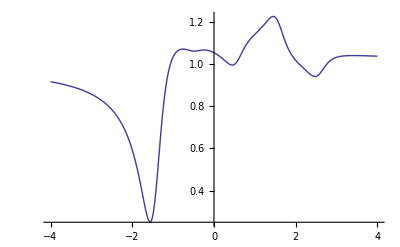

```mathematica
Plot[{transmission},{Δc,-4,4},PlotRange->Automatic]
```